# Model 2: Plotting

This file contains the processing code for Model 2. Before running this file, you must have extinction time outputs from running Model 2 for each species for both time periods using Model2.nb. Edit import (‘directory’) and export (‘saveto’) locations for your own device.

## Figure 5

Code for each subfigure of figure 6. Parts a and b require only T.citricidus (or any other species), but parts c-e require the full dataset.

```mathematica
directory="/IMPORT/";
saveto="/EXPORT/";
```

### Subfigs a & b

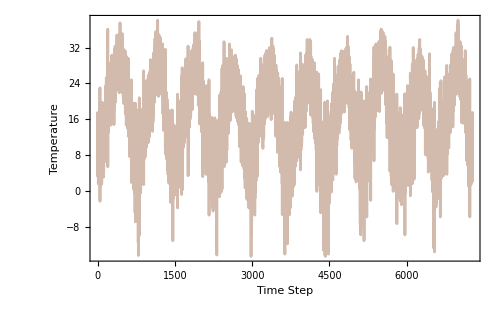

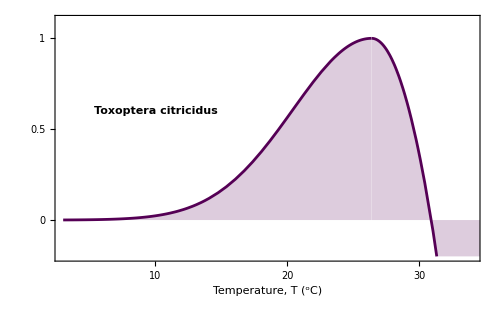

```mathematica
cmplx[mod_,arg_]:=ExpToTrig[mod Exp[I arg]];

SpecSynFourier[γ_,Nobs_,μ_:0,σ_:1,seed_:0]:=Module[{
phase,f,fseries,vec},
If[seed==0,SeedRandom[],SeedRandom[seed]];
phase=RandomReal[{0,2Pi},Nobs];
f=Range[1/Nobs,0.5,1/Nobs];
fseries=Join[{0+0I},Table[cmplx[1/f[[i]]^(γ/2 ),phase[[i]]],{i,1,Length[f]}],Table[cmplx[1/f[[i]]^(γ/2 ),-1*phase[[i]]],{i,Length[f]-1,1,-1}]];
vec=InverseFourier[fseries,FourierParameters->{-1,1}];
Standardize[Re[vec[[1;;Nobs]]]]*σ+μ];

changeautocorr[X_,γ_,samplesperyear_,seed_:0]:=Module[{
var,Y,fftdata,mean,mmeandevs,adjvar,powersp,int,lm,a,b,n=Length[X],phase,f,vec,Z},
mean=Mean[X];
var=Variance[X-mean];
mmeandevs=Table[Mean[Table[X[[i]],{i,j,n,samplesperyear}]],{j,1,samplesperyear}];
Y=Table[X[[i]]-mmeandevs[[Mod[i,samplesperyear,1]]],{i,1,n}];
adjvar=Variance[Y];
fftdata=Fourier[Y,FourierParameters->{-1,1}];
powersp=Table[{i/n,Abs[fftdata[[i+1]]]^2},{i,1,n/2-1}];
lm=LinearModelFit[{Log[#1],Log[#2]}&@@@powersp,x,x];
If[seed==0,SeedRandom[],SeedRandom[seed]];
phase=RandomReal[{0,2Pi},n];
f=Range[1/n,1,1/n];
vec=InverseFourier[Join[{0+0I},Table[cmplx[1/f[[i]]^(γ/2 ),phase[[i]]],{i,1,Length[f]}],Table[cmplx[1/f[[i]]^(γ/2 ),-1*phase[[i]]],{i,Length[f]-1,1,-1}]],FourierParameters->{-1,1}];
Z=Standardize[Re[vec]]*Sqrt[adjvar];
{{lm,var,adjvar},Table[Z[[i]]+mmeandevs[[Mod[i,samplesperyear,1]]],{i,1,n}]}
]

Mimic1[x_,z_]:=Module[{y},
y=x;
Do [y[[Ordering[z,i][[i]]]]=x[[i]],{i,1,Length[x]}];
y];

getParameters[species_String]:=Module[{row},row=SelectFirst[speciesData,#[[1]]==species&];
If[row===Missing["NotFound"],"Species not found",Rest[row]]]

species="T.citricidus";(*select species. watch out for spelling!*)
when="1994-01-01to2003-12-31"; (*1994-01-01to2003-12-31 OR 2014-01-01to2023-12-31*)

TPCdata=Import[directory<>"speciesparams.xlsx"];
speciesData=TPCdata[[1,2;;]];

parameters=getParameters[species];
CTmax=parameters[[1]];
Topt=parameters[[2]];
σp=parameters[[3]];
lat=ToString[parameters[[4]]];
long=ToString[parameters[[5]]];
name=parameters[[14]];

data=Import[directory<>"VisualCrossingData/"<>species<>"_"<>lat<>","<>long<>"_"<>when<>".csv","CSV"]; 
temps=Flatten[data[[2;;,{2,3}]]];
pairedTemps=Partition[temps,2]; 
meanTemps=Mean/@pairedTemps;

γ=1;
X=changeautocorr[meanTemps,γ,365,0];
W=SortBy[pairedTemps,Mean[{#[[1]],#[[2]]}]&];
Z=Mimic1[W,X[[2]]];
Z=Flatten[Z];
Z2=Select[Z,#>=-15&];(*excluding a couple of cold outliers for visibility - they are not excluded from simulations*)

tempsubplot=ListLinePlot[Z2,ColorFunction->ColorData["ThermometerColors"],Frame->{True,True,False,False},FrameStyle->14,FrameLabel->{"Time Step","Temperature"},LabelStyle->Directive[Black],ImageSize->500]

rD[T_,Topt_,σp_,CTmax_]:=If[T≤Topt,Exp[-((T-Topt)/(2σp))^2],1-((T-Topt)/(Topt-CTmax))^2]; 
TcTPC=Plot[rD[T,Topt,σp,CTmax],{T,3,35},PlotRange->{{3,34},{-.2,1.1}},AxesOrigin->{-10,0},PlotStyle->Darker[Purple],Filling->Axis,Frame->{True,False,False,True},FrameStyle->18,FrameLabel->{"Temperature, T (^oC)",None,None,"Normalized Fitness r"},LabelStyle->Directive[Black],FrameTicks->{{10,20,30},{0,0.5,1}},Epilog->{Style[Text[Style[ToString[name],FontWeight->Bold,FontSlant->Italic],{10,.6}],18]},ImageSize->500]

Export[saveto<>"tempsubplot.pdf",tempsubplot,ImageResolution->1000];
Export[saveto<>"TcitricidusTPC.pdf",TcTPC,ImageResolution->1000];
```

### Dot plot summary of results

These figures require .csvs of point locations.

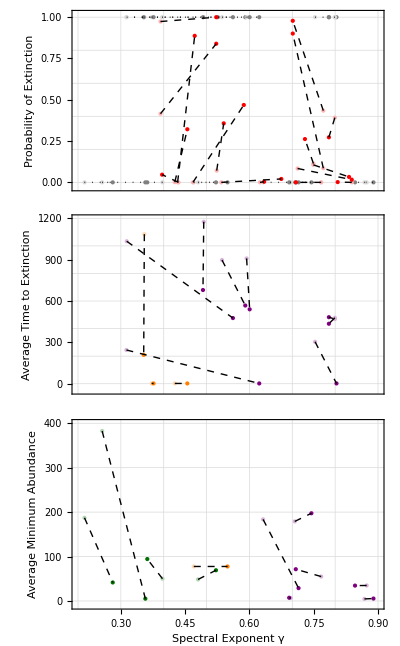

```mathematica
usefuldata=Import[directory<>"usefulpoints.csv"];
speciesData1=Rest[usefuldata];
points1=speciesData1/. {species_,hGamma_,hPExt_,pGamma_,pPExt_}:>{species,{{hGamma,hPExt},{pGamma,pPExt}}};

uselessdata=Import[directory<>"uselesspoints.csv"];
speciesData2=Rest[uselessdata];
points2=speciesData2/. {species_,hGamma_,hPExt_,pGamma_,pPExt_}:>{species,{{hGamma,hPExt},{pGamma,pPExt}}};

pext=Graphics[{Table[{PointSize[Large],LightGray,Point[points2[[i,2,1]]],Gray,Point[points2[[i,2,2]]],Black,Dotted,Line[points2[[i,2]]]},{i,1,Length[points2]}],Table[{PointSize[Large],Lighter[Lighter[Lighter[Red]]],Point[points1[[i,2,1]]],Red,Point[points1[[i,2,2]]],
Black,Dashed,Line[points1[[i,2]]]},
{i,1,Length[points1]}]},
Axes->True,AxesLabel->{"Gamma","P(ext)"},PlotRange->{{0.2,0.9},{-.03,1.02}},Frame->{True,True,False,False},FrameStyle->14,FrameLabel->{(*"Spectral Exponent γ"*)None,"Probability of Extinction"},LabelStyle->Directive[Black],
GridLines->{Range[0.2,0.9,0.1],Range[0,1,0.2]},
FrameTicks->{None,Automatic},ImageSize->500,AspectRatio->13/23];

exttimedata=Import[directory<>"fullextinctpoints.csv"];
speciesData3=Rest[exttimedata];
points3=speciesData3/. {species_,hGamma_,hPExt_,pGamma_,pPExt_}:>{species,{{hGamma,hPExt},{pGamma,pPExt}}};

exttime=Graphics[{Table[{PointSize[Large],If[i<=3,Lighter[Lighter[Lighter[Orange]]],Lighter[Lighter[Lighter[Purple]]]],Point[points3[[i,2,1]]],If[i<=3,Orange,Purple],Point[points3[[i,2,2]]],Black,Dashed,Line[points3[[i,2]]]},{i,1,Length[points3]}]},
Axes->True,AxesLabel->{"Gamma","P(ext)"},PlotRange->{{0.2,0.9},{-50,1200}},Frame->{True,True,False,False},FrameStyle->14,FrameLabel->{(*"Spectral Exponent γ"*)None,"Average Time to Extinction"},LabelStyle->Directive[Black],
GridLines->{Range[0.2,0.9,0.1],Range[0,1200,200]},
FrameTicks->{None,Automatic},ImageSize->500,AspectRatio->13/23];

minpopdata=Import[directory<>"fullpersistpoints.csv"];
speciesData4=Rest[minpopdata];
points4=speciesData4/. {species_,hGamma_,hPExt_,pGamma_,pPExt_}:>{species,{{hGamma,hPExt},{pGamma,pPExt}}};

minpop=Graphics[{Table[{PointSize[Large],If[i==1,Lighter[Lighter[Lighter[Orange]]],If[i<=5,Lighter[Lighter[Lighter[Darker[Darker[Green]]]]],Lighter[Lighter[Lighter[Purple]]]]],Point[points4[[i,2,1]]],If[i==1,Orange,If[i<=5,Darker[Darker[Green]],Purple]],Point[points4[[i,2,2]]],Black,Dashed,Line[points4[[i,2]]]},{i,1,Length[points4]}]},
Axes->True,PlotRange->{{0.2,0.9},{-10,400}},Frame->{True,True,False,False},FrameStyle->14,FrameLabel->{"Spectral Exponent γ","Average Minimum Abundance"},LabelStyle->Directive[Black],
GridLines->{Range[0.2,0.9,0.1],Range[0,400,100]},
FrameTicks->{Automatic,Automatic},ImageSize->500,AspectRatio->13/23];

pointsubplots=GraphicsGrid[{{pext},{exttime},{minpop}},Spacings->-5]

Export[saveto<>"pointsubplots.pdf",pointsubplots,ImageResolution->1000];
```

## Extended Figures

This code recreates the extended figure plot (containing TPC, temperature histograms, and extinction curves) for an individual species. Most design elements will update automatically, but ‘xloc’, ‘coordinateloc’, and ‘legendloc’ require manual aesthetic adjustments for some species.

Historical P(Ext) = 0.434311

Present P(Ext) = 0.978292

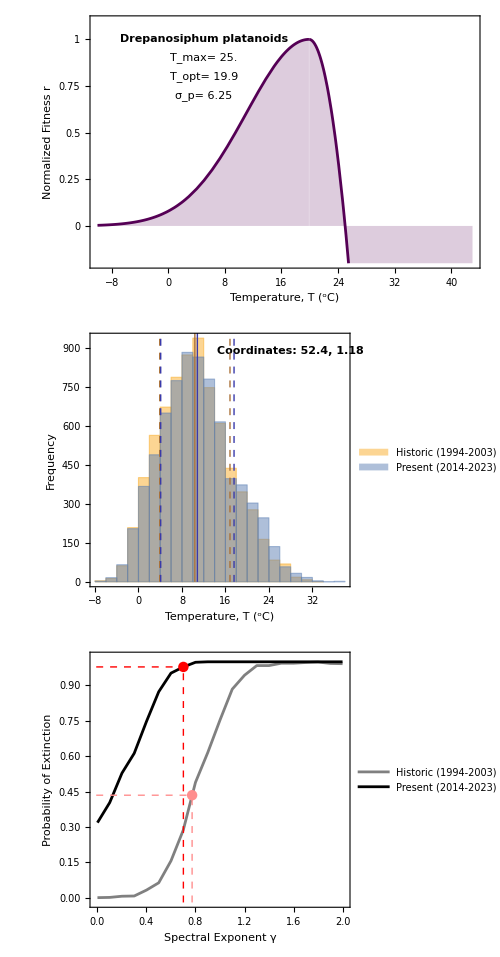

```mathematica
getParameters[species_String]:=Module[{row},row=SelectFirst[speciesData,#[[1]]==species&];
If[row===Missing["NotFound"],"Species not found",Rest[row]]]
TPCdata=Import[directory<>"speciesparams.xlsx"];
rD[T_,Topt_,σp_,CTmax_]:=If[T≤Topt,Exp[-((T-Topt)/(2σp))^2],1-((T-Topt)/(Topt-CTmax))^2]; 

species="D.platanoids";

speciesData=TPCdata[[1,2;;]];
parameters=getParameters[species];
CTmax=parameters[[1]];Topt=parameters[[2]];σp=parameters[[3]];
lat=ToString[parameters[[4]]];long=ToString[parameters[[5]]];
Hgamma=parameters[[6]];Pgamma=parameters[[7]];
Hmean=parameters[[10]];Hstdev=parameters[[11]];
Pmean=parameters[[12]];Pstdev=parameters[[13]];
name=parameters[[14]];region=parameters[[15]];

Hdata=Import[directory<>"VisualCrossingData/"<>species<>"_"<>lat<>","<>long<>"_"<>"1994-01-01to2003-12-31"<>".csv","CSV"]; 
Htemps=Flatten[Hdata[[2;;,{2,3}]]];
Pdata=Import[directory<>"VisualCrossingData/"<>species<>"_"<>lat<>","<>long<>"_"<>"2014-01-01to2023-12-31"<>".csv","CSV"]; 
Ptemps=Flatten[Pdata[[2;;,{2,3}]]];

(*subfig1: TPC*)
plotStyle=Switch[region,"NHEX",Darker[Purple],"TROP",Darker[Darker[Green]],"SHEX",Orange];

xloc=5;(*2*)
fig1=Plot[rD[T,Topt,σp,CTmax],{T,-10,43},PlotRange->{{-10,43},{-.2,1.1}},AxesOrigin->{-10,0},PlotStyle->plotStyle,Filling->Axis,Frame->{True,True,False,False},FrameStyle->14,FrameLabel->{"Temperature, T (^oC)","Normalized Fitness r"},LabelStyle->Directive[Black],FrameTicks->{Automatic,{0,0.25,0.5,0.75,1}},Epilog->{Style[Text[Style[ToString[name],FontWeight->Bold,FontSlant->Italic],{xloc,1}],14],Style[Text["T_max= "<>ToString[CTmax],{xloc,.9}],14],Style[Text["T_opt= "<>ToString[Topt],{xloc,.8}],14],
Style[Text["σ_p= "<>ToString[σp],{xloc,.7}],14]},ImageSize->500];

(*subfig2: temp histogram*)
coordinateloc={28,890};(*select depending on hist range*)
left={.18,.8};right={.8,.8};
legendloc=right;(*depending on histograms, choose where this fits*)
fig2=Histogram[{Htemps,Ptemps},Frame->{True,True,False,False},FrameStyle->14,FrameLabel->{"Temperature, T (^oC)","Frequency"},LabelStyle->Directive[Black],ChartLegends->Placed[{"Historic (1994-2003)","Present (2014-2023)"},legendloc],Epilog->{Style[Text[Style["Coordinates: "<>ToString[lat]<>", "<>ToString[long],FontWeight->Bold],coordinateloc],14],
Darker[Lighter[Orange]],Thick,Line[{{Hmean,0},{Hmean,2400}}],Darker[Lighter[Blue]],Thick,Line[{{Pmean,0},{Pmean,2400}}],
Darker[Lighter[Orange]],Dashed,Line[{{Hmean+Hstdev,0},{Hmean+Hstdev,2400}}],
Darker[Lighter[Orange]],Dashed,Line[{{Hmean-Hstdev,0},{Hmean-Hstdev,2400}}],
Darker[Lighter[Blue]],Dashed,Line[{{Pmean+Pstdev,0},{Pmean+Pstdev,2400}}],
Darker[Lighter[Blue]],Dashed,Line[{{Pmean-Pstdev,0},{Pmean-Pstdev,2400}}]
},ImageSize->500];

(*subfig3: P(ext)*)
extTimeH=Import[directory<>"Model3.3_VCoutputs/model3.3.2_"<>species<>"_1994-01-01to2003-12-31_ext1.m","MX"];
extTimeP=Import[directory<>"Model3.3_VCOutputs/model3.3.2_"<>species<>"_2014-01-01to2023-12-31_ext1.m","MX"];
maxsims=1000; γvals=Range[0,2,.1]; tmax=7300;
extMatrixH=ConstantArray[0,{Length[γvals],maxsims}];
Do[If[extTimeH[[i,l]]<tmax,extMatrixH[[i,l]]=1,extMatrixH[[i,l]]=0],
{l,1,maxsims},{i,1,Length[γvals]}]
propExtH=ConstantArray[0,{Length[γvals]}];
Do[propExtH[[i]]=Total[extMatrixH[[i]]/maxsims],
{i,1,Length[γvals]}]
propExtH=Transpose[{γvals,propExtH}];
extMatrixP=ConstantArray[0,{Length[γvals],maxsims}];
Do[If[extTimeP[[i,l]]<tmax,extMatrixP[[i,l]]=1,extMatrixP[[i,l]]=0],
{l,1,maxsims},{i,1,Length[γvals]}]
propExtP=ConstantArray[0,{Length[γvals]}];
Do[propExtP[[i]]=Total[extMatrixP[[i]]/maxsims],
{i,1,Length[γvals]}]
propExtP=Transpose[{γvals,propExtP}];

topl={.22,.85};bottomr={.8,.2};
legendloc=bottomr;(*choose based on plot*)

fig3=ListLinePlot[{propExtH,propExtP},PlotStyle->{Gray,Black},PlotRange->{{-0.02,2.02},{-.02,1.02}}, Frame->{True,True,False,False},PlotLegends->Placed[{"Historic (1994-2003)","Present (2014-2023)"},legendloc],FrameStyle->14,FrameLabel->{"Spectral Exponent γ","Probability of Extinction"},LabelStyle->Directive[Black],
Epilog->{Red,Dashed,Line[{{Pgamma,-1},{Pgamma,Interpolation[propExtP][Pgamma]}}],
Red,Dashed,Line[{{-1,Interpolation[propExtP][Pgamma]},{Pgamma,Interpolation[propExtP][Pgamma]}}],
Lighter[Lighter[Red]],Dashed,Line[{{Hgamma,-1},{Hgamma,Interpolation[propExtH][Hgamma]}}],
Lighter[Lighter[Red]],Dashed,Line[{{-1,Interpolation[propExtH][Hgamma]},{Hgamma,Interpolation[propExtH][Hgamma]}}],
{PointSize[0.015],Lighter[Lighter[Red]],Point[{Hgamma,Interpolation[propExtH][Hgamma]}]},
{PointSize[0.015],Red,Point[{Pgamma,Interpolation[propExtP][Pgamma]}]}},
ImageSize->500];

Print["Historical P(Ext) = ",Interpolation[propExtH][Hgamma]]
Print["Present P(Ext) = ",Interpolation[propExtP][Pgamma]]

(*combined=GraphicsGrid[{{fig1,fig2,fig3}},Spacings->{0,0},ImageSize->1500]*)
combinedpdf=GraphicsColumn[{fig1,fig2,fig3},Spacings->{0,0},ImageSize->500]

Export[saveto<>species<>"_all.pdf",combined,ImageResolution->1000];
```

This code recreates plots of mean time to extinction for individual species that went extinct under 100% of scenarios.

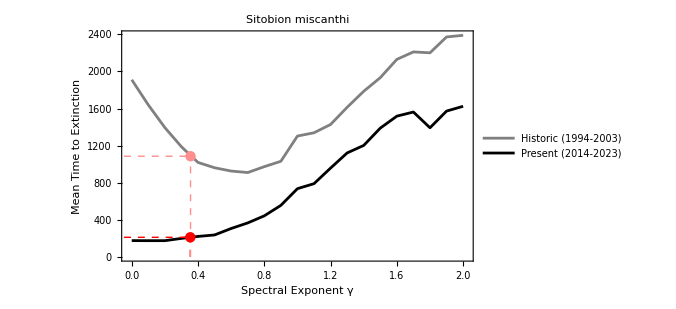

Historical ExtTime = 1084.68

Present ExtTime = 209.331

```mathematica
getParameters[species_String]:=Module[{row},row=SelectFirst[speciesData,#[[1]]==species&];
If[row===Missing["NotFound"],"Species not found",Rest[row]]]
TPCdata=Import[directory<>"speciesparams.xlsx"];

species="S.miscanthi";
extTimeH=Import[directory<>"Model3.3_VCoutputs/model3.3.2_"<>species<>"_1994-01-01to2003-12-31_ext1.m","MX"];
extTimeP=Import[directory<>"Model3.3_VCOutputs/model3.3.2_"<>species<>"_2014-01-01to2023-12-31_ext1.m","MX"];
speciesData=TPCdata[[1,2;;]];
parameters=getParameters[species];
Hgamma=parameters[[6]];
Pgamma=parameters[[7]];
name=parameters[[14]];

γvals=Range[0,2,.1];

extTimeMatrixH=ConstantArray[0,Length[γvals]];
Do[extTimeMatrixH[[i]]=Mean[extTimeH[[i]]],{i,1,Length[γvals]}]
extTimesH=Transpose[{γvals,extTimeMatrixH}];

extTimeMatrixP=ConstantArray[0,Length[γvals]];
Do[extTimeMatrixP[[i]]=Mean[extTimeP[[i]]],{i,1,Length[γvals]}]
extTimesP=Transpose[{γvals,extTimeMatrixP}];

extTimePlot=ListLinePlot[{extTimesH,extTimesP},PlotStyle->{Gray,Black},PlotRange->{{-0.02,2.02},Automatic},Frame->{True,True,False,False},PlotLabel->Style[Text[Style[ToString[name],FontWeight->Bold,FontSlant->Italic]]],PlotLegends->Placed[{"Historic (1994-2003)","Present (2014-2023)"},{.8,.2}],FrameStyle->14,FrameLabel->{"Spectral Exponent γ","Mean Time to Extinction"},LabelStyle->Directive[Black],
Epilog->{Red,Dashed,Line[{{Pgamma,-1},{Pgamma,Interpolation[extTimesP][Pgamma]}}],
Red,Dashed,Line[{{-1,Interpolation[extTimesP][Pgamma]},{Pgamma,Interpolation[extTimesP][Pgamma]}}],
Lighter[Lighter[Red]],Dashed,Line[{{Hgamma,-1},{Hgamma,Interpolation[extTimesH][Hgamma]}}],
Lighter[Lighter[Red]],Dashed,Line[{{-1,Interpolation[extTimesH][Hgamma]},{Hgamma,Interpolation[extTimesH][Hgamma]}}],
{PointSize[0.015],Lighter[Lighter[Red]],Point[{Hgamma,Interpolation[extTimesH][Hgamma]}]},
{PointSize[0.015],Red,Point[{Pgamma,Interpolation[extTimesP][Pgamma]}]}},ImageSize->500]

Print["Historical ExtTime = ",Interpolation[extTimesH][Hgamma]]
Print["Present ExtTime = ",Interpolation[extTimesP][Pgamma]]

Export[saveto<>"Model3.3_graphs/extTime/"<>species<>".pdf",extTimePlot,ImageResolution->1000];
```

This code recreates plots of average minimum abundance for individual species that went extinct under 0% of scenarios.

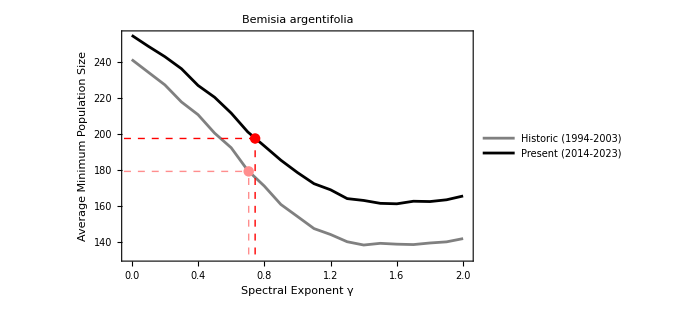

Historical Minimum Pop Size = 179.056

Present Minimum Pop Size = 197.359

```mathematica
getParameters[species_String]:=Module[{row},row=SelectFirst[speciesData,#[[1]]==species&];
If[row===Missing["NotFound"],"Species not found",Rest[row]]]
TPCdata=Import[directory<>"speciesparams.xlsx"];

species="B.argentifolia";
minPopH=Import[directory<>"Model3.3_VCoutputs/model3.3_minpop/model3.3.3_minPop_"<>species<>"_1994-01-01to2003-12-31_ext1.m","MX"];
minPopP=Import[directory<>"Model3.3_VCOutputs/model3.3_minpop/model3.3.3_minPop_"<>species<>"_2014-01-01to2023-12-31_ext1.m","MX"];
speciesData=TPCdata[[1,2;;]];
parameters=getParameters[species];
Hgamma=parameters[[6]];
Pgamma=parameters[[7]];
name=parameters[[14]];

γvals=Range[0,2,.1];

minPopMatrixH=ConstantArray[0,Length[γvals]];
Do[minPopMatrixH[[i]]=Mean[minPopH[[i]]],{i,1,Length[γvals]}]
minPopsH=Transpose[{γvals,minPopMatrixH}];

minPopMatrixP=ConstantArray[0,Length[γvals]];
Do[minPopMatrixP[[i]]=Mean[minPopP[[i]]],{i,1,Length[γvals]}]
minPopsP=Transpose[{γvals,minPopMatrixP}];

minPopPlot=ListLinePlot[{minPopsH,minPopsP},PlotStyle->{Gray,Black},PlotRange->{{-0.02,2.02},Automatic},Frame->{True,True,False,False},PlotLabel->Style[Text[Style[ToString[name],FontWeight->Bold,FontSlant->Italic]]],PlotLegends->Placed[{"Historic (1994-2003)","Present (2014-2023)"},{.8,.2}],FrameStyle->14,FrameLabel->{"Spectral Exponent γ","Average Minimum Population Size"},LabelStyle->Directive[Black],
Epilog->{Red,Dashed,Line[{{Pgamma,-1},{Pgamma,Interpolation[minPopsP][Pgamma]}}],
Red,Dashed,Line[{{-1,Interpolation[minPopsP][Pgamma]},{Pgamma,Interpolation[minPopsP][Pgamma]}}],
Lighter[Lighter[Red]],Dashed,Line[{{Hgamma,-1},{Hgamma,Interpolation[minPopsH][Hgamma]}}],
Lighter[Lighter[Red]],Dashed,Line[{{-1,Interpolation[minPopsH][Hgamma]},{Hgamma,Interpolation[minPopsH][Hgamma]}}],
{PointSize[0.015],Lighter[Lighter[Red]],Point[{Hgamma,Interpolation[minPopsH][Hgamma]}]},
{PointSize[0.015],Red,Point[{Pgamma,Interpolation[minPopsP][Pgamma]}]}},ImageSize->500]

Print["Historical Minimum Pop Size = ",Interpolation[minPopsH][Hgamma]]
Print["Present Minimum Pop Size = ",Interpolation[minPopsP][Pgamma]]

Export[saveto<>"Model3.3_graphs/minPop/"<>species<>".pdf",minPopPlot,ImageResolution->1000];
```

This code allows you to extract the spectral exponent and, if desired, plot the spectral density of any of the temperature time series.

2.63409-0.397055 x

2.27987-0.36167 x

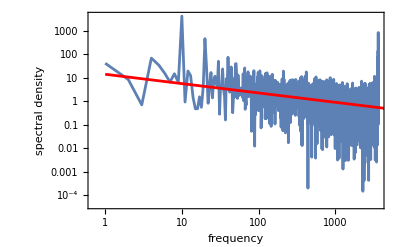

```mathematica
getParameters[species_String]:=Module[{row},row=SelectFirst[speciesData,#[[1]]==species&];
If[row===Missing["NotFound"],"Species not found",Rest[row]]]

TPCdata=Import[directory<>"speciesparams.xlsx"];
speciesData=TPCdata[[1,2;;]];
species="C.shadabi";
historic="1994-01-01to2003-12-31";
present="2014-01-01to2023-12-31";

parameters=getParameters[species];
lat=ToString[parameters[[4]]];
long=ToString[parameters[[5]]];

data=Import[directory<>"VisualCrossingData/"<>species<>"_"<>lat<>","<>long<>"_"<>historic<>".csv","CSV"]; 
temps=Flatten[data[[2;;,{2,3}]]];
lt=Flatten[Abs[Fourier[{temps}]]^2];
lt=Drop[lt,-Length[lt]/2];
lt=Drop[lt,1];
lt0=MapIndexed[{#2[[1]],#1}&,lt];
fit0=Fit[Log[lt0],{1,x},x]

data=Import[directory<>"VisualCrossingData/"<>species<>"_"<>lat<>","<>long<>"_"<>present<>".csv","CSV"]; 
temps=Flatten[data[[2;;,{2,3}]]];
lt=Flatten[Abs[Fourier[{temps}]]^2];
lt=Drop[lt,-Length[lt]/2];
lt=Drop[lt,1];
lt0=MapIndexed[{#2[[1]],#1}&,lt];
fit0=Fit[Log[lt0],{1,x},x]

Show[ListLinePlot[lt,ScalingFunctions->{"Log","Log"},Frame->True,FrameLabel->{"frequency","spectral density"}],
Plot[2.6340898511613706-0.3970554074582351x,{x,0,tmax},PlotStyle->Red]]
```

## Bar chart summary of results

This code recreates Fig 5c and d.

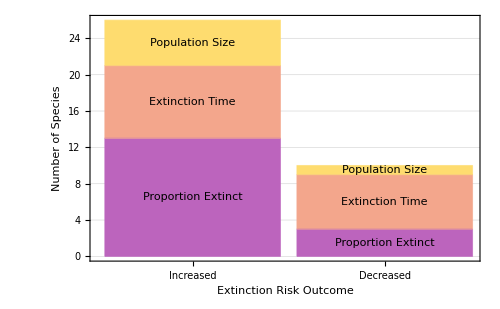

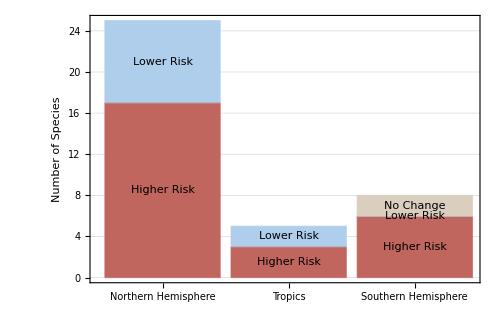

```mathematica
outcomebars=BarChart[{{13,8,5},{3,6,1}},ChartLayout->"Stacked",ChartStyle->{Lighter[RGBColor["#9a169c"]],Lighter[RGBColor["#ed7953"]],Lighter[RGBColor["#fdca27"]]},
ChartLabels->{{"Increased","Decreased"},{"Proportion Extinct","Extinction Time","Population Size"}},PlotTheme->"Detailed",ImageSize->500,FrameLabel->{"Extinction Risk Outcome","Number of Species"},FrameStyle->16,"FixedBarSpacing"->True]

regionbars=BarChart[{{17,8},{3,2},{6,0,2}},ChartLayout->"Stacked",ChartStyle->{RGBColor["#c0665e"],RGBColor["#aeceeb"],RGBColor["#dacfbe"]},ChartLabels->{{"Northern\n Hemisphere","Tropics","Southern\n Hemisphere"},{"Higher Risk","Lower Risk","No Change"}},PlotTheme->"Detailed",ImageSize->500,FrameLabel->{None,"Number of Species"},FrameStyle->16,"FixedBarSpacing"->True]

Export[saveto<>"barchart_outcome.pdf",outcomebars,ImageResolution->1000];
Export[saveto<>"barchart_region.pdf",regionbars,ImageResolution->1000];
```